```mathematica
Clear[a01t,a02t]
a01t=Alpha0t[1];
a02t=Alpha0t[2];
```

```mathematica
{{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}.{{s11Q,s12Q},{s12Q,s22Q}}.{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}}
```

p0normal: 1.42592

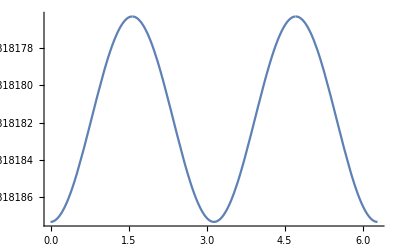

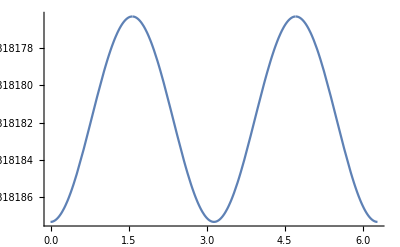

1.42592

```mathematica
Clear[q,dalpha,s11Q,s12Q,s22Q,z,t,r,eta,Xi,g,rrt,p0normal]
q=1;
p0normal=1./((1+Nu0)/Mu0 +Mu0(1+Nu[1])/MuQ[q] );
Print["p0normal: ",p0normal]
dalpha= ThermalExpansionQ[q]-ThermalExpansion0;
g=0.5/(Mu0*dalpha); (*beta in 2D can be written as beta=alpha, where alpha is expansion coefficiens for 2D. Or it can be written as beta=2alpha, and alpha is a 1D expansion coefficients. Here our alpha is for 1D, this, we have to divid it with 2.*)



(*s11Q=Sigma11ztot;
s12Q=Sigma12ztot;
s22Q=Sigma22ztot;*)
s11Q=Sigma11m[q];
s12Q=Sigma12m[q];
s22Q=Sigma22m[q];
r={{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}.{{s11Q,s12Q},{s12Q,s22Q}}.{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}};
rrr=s11Q*Cos[t]*Cos[t]+s22Q*Sin[t]*Sin[t]+s12Q*Sin[2*t];

z=dd[q]Cosh[Xi];
rrt=Tau0[q];
Xi=Zeta0[q]+I*eta;
t=eta;-I*Log[(dd [q]Cos[eta-ⅈ Zeta0[q]])/l1[q]];

Plot[r[[1,1]]*g,{eta,-0,2Pi}]
Plot[Re[rrt]*g,{eta,-0,2Pi}]

(*Plot[r[[1,2]]*g,{eta,-0,2Pi}]

Plot[r[[2,2]]*g,{eta,-0,2Pi}]*)
```

```mathematica
eta=Pi/2;
s22Q/(Mu0*dalpha)/4
```

-1.27751

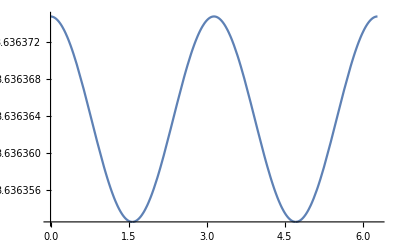

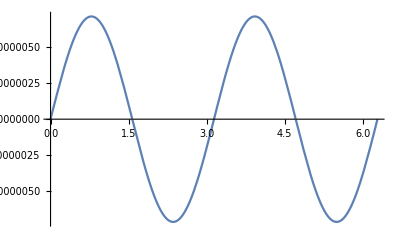

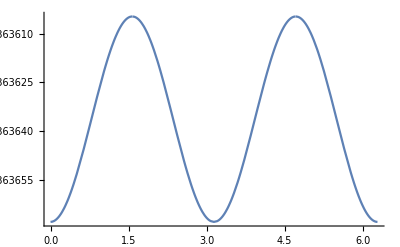

```mathematica
Clear[z,Xi]
z=dd[q]Cosh[Xi];
r={{Cos[t],Sin[t]},{-Sin[t],Cos[t]}}.{{s11Q,s12Q},{s12Q,s22Q}}.{{Cos[t],-Sin[t]},{Sin[t],Cos[t]}};
rrr=s11Q*Cos[t]*Cos[t]+s22Q*Sin[t]*Sin[t]+s12Q*Sin[2*t];
Xi=Zeta0[q]+I*eta;
t=eta;-I*Log[(dd [q]Cos[eta-ⅈ Zeta0[q]])/l1[q]];
Plot[r[[1,1]]/(Mu0*dalpha),{eta,-0,2Pi}]

Plot[r[[1,2]]/(Mu0*dalpha),{eta,-0,2Pi}]

Plot[r[[2,2]]/(Mu0*dalpha),{eta,-0,2Pi}]
```

```mathematica
Clear[p0,s, beta0]
p0=1./((1+Nu00)/E00  + (1-NuQ0)/EQ0 )
```

1./((1+Nu00)/E00+(1-NuQ0)/EQ0)

```mathematica
s=0.5*beta0 /(E00/(1-nu00));
beta0 = alph*E00/(1-nu00);
Simplify[s]
```

0.5 alph

```mathematica
p0
```

1./((1+Nu00)/E00+(1-NuQ0)/EQ0)

```mathematica
q=1;
dalpha=ThermalExpansion0-ThermalExpansionQ[q];
dtem=1;
p=1/((1+Nu0)/E0+(1-Nu[q])/EQ[q])
```

1647.06

```mathematica
1./((1+Nu0)/(2.*Mu0(1+Nu0))+(1-Nu[q])/(2.*MuQ[q](1+Nu[q])))
```

1647.06

```mathematica
?E0
```

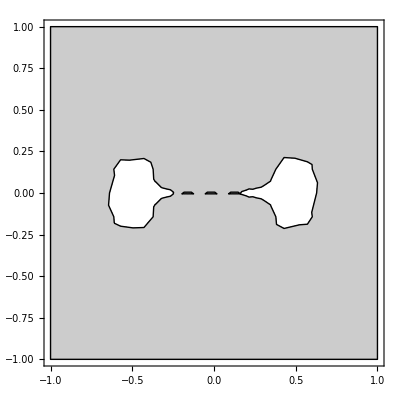

```mathematica
Clear[size]
Clear[q,s11Q,s12Q,s22Q,z,eta,Xi,g]
q=1;c1=10;
s11Q=Sigma11m[q];
s12Q=Sigma12m[q];
s22Q=Sigma22m[q];
smv= Sqrt[s11Q*s11Q+s22Q*s22Q-s11Q*s22Q+3s12Q*s12Q];

dalpha= ThermalExpansionQ[q]-ThermalExpansion0;
g=0.5/(Mu0*dalpha);

size=2l1[1];
Xi=XiQ[q];
z=x+I*y;

ContourPlot[smv*g,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,PlotRange->Automatic,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]
```

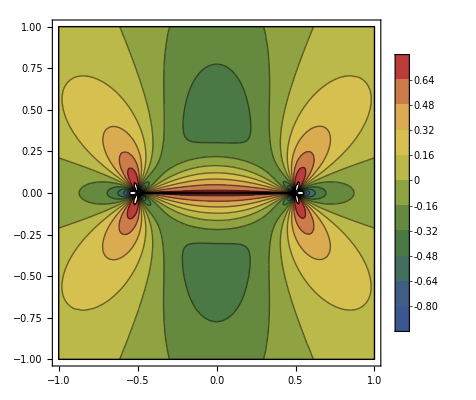

```mathematica
Clear[size]
Clear[q,s11Q,s12Q,s22Q,z,eta,Xi,g]
q=1;c1=10;
s11Q=Sigma11m[q];
s12Q=Sigma12m[q];
s22Q=Sigma22m[q];
smv= Sqrt[s11Q*s11Q+s22Q*s22Q-s11Q*s22Q+3s12Q*s12Q];

dalpha= ThermalExpansionQ[q]-ThermalExpansion0;
g=0.5/(Mu0*dalpha);

size=2l1[1];
Xi=XiQ[q];
z=x+I*y;
ContourPlot[s22Q,{x,-size,size},{y,-size,size},BoundaryStyle->Black,ContourLabels->False, PlotLegends->Automatic,Exclusions->None,ColorFunction->"DarkRainbow",Contours->c1,PlotRange->Automatic,RegionFunction->Function[{x,y,z},(((x-Re[zcenter[q]]) Cos[Theta[q]]+(y-Im[zcenter[q]]) Sin[Theta[q]])/l1[q])^2. + (((x-Re[zcenter[q]]) Sin[Theta[q]]-(y-Im[zcenter[q]])Cos[Theta[q]])/l2[q])^2.>=1]]
```